```mathematica
Needs["qi`"];
eps=LeviCivitaTensor[3]
```

SetDelayed::write: Tag SquareMatrixQ in SquareMatrixQ[A_] is Protected.

Package QI version 0.4.37 (last modification: 21/12/2012).

Needs::nocont: Context "qi`" was not created when Needs was evaluated.

SparseArray[<6>, {3, 3, 3}]

```mathematica
Roots[3x^4+6x^2-1==0,x]
```

x==-1/3||x==1||x==1||x==1

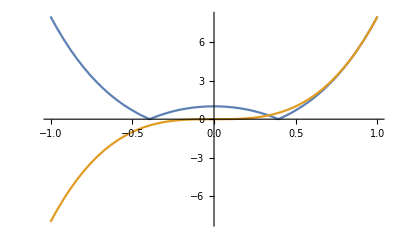

```mathematica
Plot[{Abs[3x^4+6x^2-1],8x^3},{x,-1,1}]
```

```mathematica
Roots[-3x^4-8x^3-6x^2+1==0,x]
```

x==1/3||x==-1||x==-1||x==-1

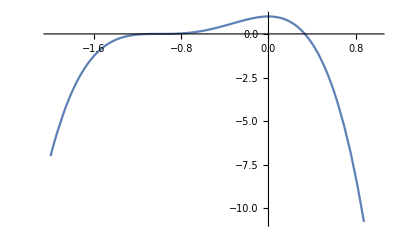

```mathematica
Plot[-3x^4-8x^3-6x^2+1,{x,-2,1}]
```

```mathematica
Roots[-3x^4+8x^3-6x^2+1==0,x]
```

x==-1/3||x==1||x==1||x==1

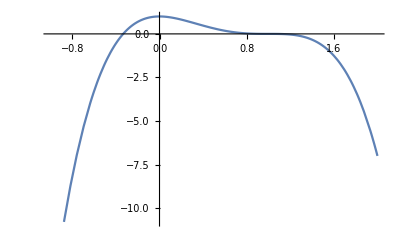

```mathematica
Plot[-3x^4+8x^3-6x^2+1,{x,-1,2}]
```

```mathematica
Roots[2x^3-3x^2+1==0,x]
```

x==-1/2||x==1||x==1

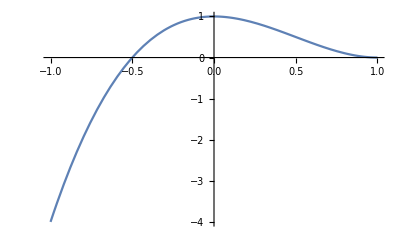

```mathematica
Plot[2x^3-3x^2+1,{x,-1,1}]
```

```mathematica
Clear[x]
```

```mathematica
Roots[-2x^3-3x^2+1==0,x]
```

x==1/2||x==-1||x==-1

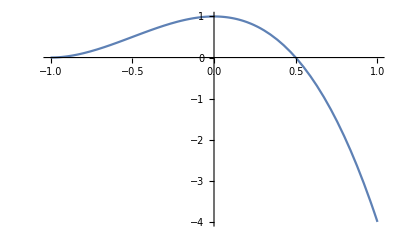

```mathematica
Plot[-2x^3-3x^2+1,{x,-1,1}]
```

```mathematica
rho1={{1-y,0,0,0},{0,y+1,-2y,0},{0,-2y,y+1,0},{0,0,0,1-y}}/4
```

((1-y)/4 | 0 | 0 | 0
0 | (1+y)/4 | -y/2 | 0
0 | -y/2 | (1+y)/4 | 0
0 | 0 | 0 | (1-y)/4)

```mathematica
Eigenvalues[rho1]
```

{(1-y)/4,(1-y)/4,(1-y)/4,1/4 (1+3 y)}

```mathematica
rho1t={{1-y,0,0,-2y},{0,y+1,0,0},{0,0,y+1,0},{-2y,0,0,1-y}}/4
```

((1-y)/4 | 0 | 0 | -y/2
0 | (1+y)/4 | 0 | 0
0 | 0 | (1+y)/4 | 0
-y/2 | 0 | 0 | (1-y)/4)

```mathematica
Eigenvalues[rho1t]
```

{1/4 (1-3 y),(1+y)/4,(1+y)/4,(1+y)/4}

```mathematica
rho2={{1-y,0,0,0},{0,y+1,2y,0},{0,2y,y+1,0},{0,0,0,1-y}}/4
```

((1-y)/4 | 0 | 0 | 0
0 | (1+y)/4 | y/2 | 0
0 | y/2 | (1+y)/4 | 0
0 | 0 | 0 | (1-y)/4)

```mathematica
Eigenvalues[rho2]
```

{(1-y)/4,(1-y)/4,(1-y)/4,1/4 (1+3 y)}

```mathematica
rho2t={{1-y,0,0,2y},{0,y+1,0,0},{0,0,y+1,0},{2y,0,0,1-y}}/4
```

((1-y)/4 | 0 | 0 | y/2
0 | (1+y)/4 | 0 | 0
0 | 0 | (1+y)/4 | 0
y/2 | 0 | 0 | (1-y)/4)

```mathematica
Eigenvalues[rho2t]
```

```mathematica
{1/4 (1-3 y),(1+y)/4,(1+y)/4,(1+y)/4}
```

```mathematica
s={{n1,n2-I*n3},{n2+I*n3,-n1}}
```

(n1 | n2-ⅈ n3
n2+ⅈ n3 | -n1)

```mathematica
Eigenvalues[s]
```

{-√(n1^2+n2^2+n3^2),√(n1^2+n2^2+n3^2)}

```mathematica
Eigenvectors[s]
```

(-(-n1+√(n1^2+n2^2+n3^2))/(n2+ⅈ n3) | 1
-(-n1-√(n1^2+n2^2+n3^2))/(n2+ⅈ n3) | 1)

```mathematica
u1=Normalize[{4,5,4}]
```

{4/(√57),5/(√57),4/(√57)}

```mathematica
v1=Normalize[{1,-2,4}]
```

{1/(√21),-2/(√21),4/(√21)}

```mathematica
P=u1.Transpose[v1]
```

```mathematica
Transpose[v1]
```

Transpose[{1/(√21),-2/(√21),4/(√21)}]

```mathematica
Row[v1]
```

1/(√21)-2/(√21)4/(√21)

```mathematica
u2=
```

```mathematica
P=Outer[Times,u1,v1]
```

{{4/(3 √133),-8/(3 √133),16/(3 √133)},{5/(3 √133),-10/(3 √133),20/(3 √133)},{4/(3 √133),-8/(3 √133),16/(3 √133)}}

```mathematica
Det[P]
```

0

```mathematica
Eigenvalues[P]
```

{10/(3 √133),0,0}

```mathematica
Eigenvectors[P]
```

{{4,5,4},{-4,0,1},{2,1,0}}

```mathematica
u2=Normalize[{-3,0,2}]
```

{-3/(√13),0,2/(√13)}

```mathematica
v2=Normalize[{3,4,5}]
```

{3/(5 √2),(2 √2)/5,1/(√2)}

```mathematica
P2=Outer[Times,u1,v1]+Outer[Times,u2,v2]
```

{{-9/(5 √26)+4/(3 √133),-(6 √(2/13))/5-8/(3 √133),-3/(√26)+16/(3 √133)},{5/(3 √133),-10/(3 √133),20/(3 √133)},{(3 √(2/13))/5+4/(3 √133),(4 √(2/13))/5-8/(3 √133),√(2/13)+16/(3 √133)}}

```mathematica
Eigenvalues[P2]
```

{(399 √26+1300 √133+√(51870000 √3458+(399 √26+1300 √133)^2))/103740,(399 √26+1300 √133-√(51870000 √3458+(399 √26+1300 √133)^2))/103740,0}

```mathematica
Eigenvectors[P2]
```

{{-(-15227+1590 √3458-20 √(26 (66197+15300 √3458))+27 √(133 (66197+15300 √3458)))/(2 (16591+1980 √3458+10 √(26 (66197+15300 √3458))+9 √(133 (66197+15300 √3458)))),(25 (1300+87 √3458+√(26 (66197+15300 √3458))))/(2 (16591+1980 √3458+10 √(26 (66197+15300 √3458))+9 √(133 (66197+15300 √3458)))),1},{-(-15227+1590 √3458+20 √(26 (66197+15300 √3458))-27 √(133 (66197+15300 √3458)))/(2 (16591+1980 √3458-10 √(26 (66197+15300 √3458))-9 √(133 (66197+15300 √3458)))),(25 (1300+87 √3458-√(26 (66197+15300 √3458))))/(2 (16591+1980 √3458-10 √(26 (66197+15300 √3458))-9 √(133 (66197+15300 √3458)))),1},{-13/5,7/10,1}}

```mathematica
a={{1,1},{0,1}};
```

```mathematica
Eigenvalues[a]
```

{1,1}

```mathematica
Eigenvectors[a]
```

{{1,0},{0,0}}

```mathematica
ClearAll
```

ClearAll

```mathematica
r={Subscript[f, 1],Subscript[f, 2],Subscript[f, 3]}
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[f_1]

```mathematica
a={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}
```

{{{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_1,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_2,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_3}_1,{{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_1,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_2,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_3}_2,{{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_1,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_2,{{a1,a2,a3}_1,{a1,a2,a3}_2,{a1,a2,a3}_3}_3}_3}

```mathematica
KroneckerProduct[a,a]
```

(a1^2 | a1 a2 | a1 a3
a1 a2 | a2^2 | a2 a3
a1 a3 | a2 a3 | a3^2)

```mathematica
mat={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}
```

{x_1,x_2,x_3}

```mathematica
z=mat
```

{x_1,x_2,x_3}

```mathematica
sq=KroneckerProduct[z,z]
```

{{x_1^2,x_1 x_2,x_1 x_3},{x_1 x_2,x_2^2,x_2 x_3},{x_1 x_3,x_2 x_3,x_3^2}}

```mathematica
A={{0,-Subscript[x, 3],Subscript[x, 2]},{Subscript[x, 3],0,-Subscript[x, 1]},{Subscript[x, 2],Subscript[x, 1],0}}
```

{{0,-x_3,x_2},{x_3,0,-x_1},{x_2,x_1,0}}

```mathematica
id=IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
sq+Subscript[c, 1]*(id-sq)+Subscript[s, 1]*A
```

{{x_1^2+c_1 (1-x_1^2),x_1 x_2-c_1 x_1 x_2-s_1 x_3,s_1 x_2+x_1 x_3-c_1 x_1 x_3},{x_1 x_2-c_1 x_1 x_2+s_1 x_3,x_2^2+c_1 (1-x_2^2),-s_1 x_1+x_2 x_3-c_1 x_2 x_3},{s_1 x_2+x_1 x_3-c_1 x_1 x_3,s_1 x_1+x_2 x_3-c_1 x_2 x_3,x_3^2+c_1 (1-x_3^2)}}

```mathematica
P=Array[Subscript[p,#1,#2]&,{3,3}]
```

{{p_(1,1),p_(1,2),p_(1,3)},{p_(2,1),p_(2,2),p_(2,3)},{p_(3,1),p_(3,2),p_(3,3)}}

```mathematica
Simplify[Tr[P.A]]
```

x_3 (p_(1,2)-p_(2,1))+x_2 (p_(1,3)+p_(3,1))+x_1 (p_(2,3)-p_(3,2))

```mathematica
Clear[f]
```

```mathematica
f[x_,a_]:=Module[{z,sq,cross,c,s},
(*z=Array[Subscript[x,#1]&,{3}];*)
sq=KroneckerProduct[x,x];
cross={{0,-x[[3]],x[[2]]},{x[[3]],0,-x[[1]]},{x[[2]],x[[1]],0}};
sq+Cos[a]*(id-sq)+Sin[a]*cross]
```

```mathematica
Clear[a,c,s,i,b]
```

```mathematica
f[a,α ]
```

(a_1^2+cos(α) (1-a_1^2) | -cos(α) a_1 a_2+a_1 a_2-sin(α) a_3 | sin(α) a_2-cos(α) a_1 a_3+a_1 a_3
-cos(α) a_1 a_2+a_1 a_2+sin(α) a_3 | a_2^2+cos(α) (1-a_2^2) | -sin(α) a_1-cos(α) a_2 a_3+a_2 a_3
sin(α) a_2-cos(α) a_1 a_3+a_1 a_3 | sin(α) a_1-cos(α) a_2 a_3+a_2 a_3 | a_3^2+cos(α) (1-a_3^2))

```mathematica
Clear[a]
```

```mathematica
x={Subscript[a, 1],Subscript[a, 2],Sqrt[Subscript[a, 1]^2+Subscript[a, 2]^2]}
```

{a_1,a_2,√(a_1^2+a_2^2)}

```mathematica
x[[1]]
```

a_1

```mathematica
Clear[b]
```

```mathematica
y={Subscript[b, 1],Subscript[b, 2],Sqrt[Subscript[b, 1]^2+Subscript[b, 2]^2]}
```

```mathematica
{Subscript[b, 1],Subscript[b, 2],√(Subscript[b, 1]^2+Subscript[b, 2]^2)}
```

```mathematica
m1=f[x,α ]
```

(a_1^2+cos(α) (1-a_1^2) | -√(a_1^2+a_2^2) sin(α)-cos(α) a_1 a_2+a_1 a_2 | -cos(α) √(a_1^2+a_2^2) a_1+√(a_1^2+a_2^2) a_1+sin(α) a_2
√(a_1^2+a_2^2) sin(α)-cos(α) a_1 a_2+a_1 a_2 | a_2^2+cos(α) (1-a_2^2) | -sin(α) a_1-cos(α) a_2 √(a_1^2+a_2^2)+a_2 √(a_1^2+a_2^2)
-cos(α) √(a_1^2+a_2^2) a_1+√(a_1^2+a_2^2) a_1+sin(α) a_2 | sin(α) a_1-cos(α) a_2 √(a_1^2+a_2^2)+a_2 √(a_1^2+a_2^2) | a_1^2+a_2^2+cos(α) (-a_1^2-a_2^2+1))

```mathematica
m3=f[x,-α ]
```

(a_1^2+cos(α) (1-a_1^2) | √(a_1^2+a_2^2) sin(α)-cos(α) a_1 a_2+a_1 a_2 | -cos(α) √(a_1^2+a_2^2) a_1+√(a_1^2+a_2^2) a_1-sin(α) a_2
-√(a_1^2+a_2^2) sin(α)-cos(α) a_1 a_2+a_1 a_2 | a_2^2+cos(α) (1-a_2^2) | sin(α) a_1-cos(α) a_2 √(a_1^2+a_2^2)+a_2 √(a_1^2+a_2^2)
-cos(α) √(a_1^2+a_2^2) a_1+√(a_1^2+a_2^2) a_1-sin(α) a_2 | -sin(α) a_1-cos(α) a_2 √(a_1^2+a_2^2)+a_2 √(a_1^2+a_2^2) | a_1^2+a_2^2+cos(α) (-a_1^2-a_2^2+1))

```mathematica
m2=f[y,β ]
```

(b_1^2+cos(β) (1-b_1^2) | -√(b_1^2+b_2^2) sin(β)-cos(β) b_1 b_2+b_1 b_2 | -cos(β) √(b_1^2+b_2^2) b_1+√(b_1^2+b_2^2) b_1+sin(β) b_2
√(b_1^2+b_2^2) sin(β)-cos(β) b_1 b_2+b_1 b_2 | b_2^2+cos(β) (1-b_2^2) | -sin(β) b_1-cos(β) b_2 √(b_1^2+b_2^2)+b_2 √(b_1^2+b_2^2)
-cos(β) √(b_1^2+b_2^2) b_1+√(b_1^2+b_2^2) b_1+sin(β) b_2 | sin(β) b_1-cos(β) b_2 √(b_1^2+b_2^2)+b_2 √(b_1^2+b_2^2) | b_1^2+b_2^2+cos(β) (-b_1^2-b_2^2+1))

```mathematica
this={{1,1,0},{0,1,1},{0,0,1}}
```

(1 | 1 | 0
0 | 1 | 1
0 | 0 | 1)

```mathematica
Tr[this.Transpose[this]]
```

5

```mathematica
Eigensystem[this]
```

{{1,1,1},{{1,0,0},{0,0,0},{0,0,0}}}

```mathematica
Eigenvalues[this]
```

{1,1,1}

```mathematica
levi=LeviCivitaTensor[3]
```

SparseArray[<6>, {3, 3, 3}]

```mathematica
v=Normalize[{1,3,-2}]
```

{1/(√14),3/(√14),-√(2/7)}

```mathematica
vc=levi.v
```

(0 | -√(2/7) | -3/(√14)
√(2/7) | 0 | 1/(√14)
3/(√14) | -1/(√14) | 0)

```mathematica
Det[vc]
```

0

```mathematica
Eigenvalues[vc]
```

{ⅈ,-ⅈ,0}

```mathematica
N[2/Pi]
```

0.63662

```mathematica
N[(8/Pi^2-1)^2-4*16/Pi^4]
```

-0.621139

```mathematica
paulis=GeneralizedPauliMatrices[2];
```

```mathematica
sx
```

(0 | 1
1 | 0)

```mathematica
sy
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
rho=IdentityMatrix[4]+(KroneckerProduct[sx,sx]+KroneckerProduct[sy,sy])*2/Pi
```

(1 | 0 | 0 | 0
0 | 1 | 4/π | 0
0 | 4/π | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Eigensystem[rho]
```

{{(4+π)/π,1,1,(-4+π)/π},{{0,-1,-1,0},{0,0,0,1},{1,0,0,0},{0,-1,1,0}}}

```mathematica
{2,1,1,0}
```

{2,1,1,0}